## Mitosis

We model the change in the distribution of the number of mutations at a single locus, k, in a population as a result of selection, mutation and reproduction by mitosis.

## Model

### Parameters

k, number of mutations
f_k, frequency of genotype with k mutations
k̄, mean number of mutations
𝒱, variance in the number of mutations
𝒮, third central moment (skewness) of the number of mutations
n, ploidy
s, effect of a mutation if present in n copies (s < 0 if mutations are deleterious)
w, fitness
w̄, mean fitness
ŵ, mean fitness at equilibrium
u, mutation rate per locus (haploid)

### Statistics

#### Genotype frequencies

```mathematica
f[n_]:=Table[Subscript[f, k],{k,0,n}]
```

```mathematica
f[3]
```

{f_0,f_1,f_2,f_3}

```mathematica
cum[n_]:=1-∑_(k=0)^(n-1) Subscript[f, k]
```

```mathematica
cum[3]
```

1-f_0-f_1-f_2

#### Mean number of mutations

```mathematica
k̄[n_]:=Total[f[n]Table[k,{k,0,n}]]
```

```mathematica
k̄[4]
```

f_1+2 f_2+3 f_3+4 f_4

```mathematica
k̄[4]/.{Subscript[f, 4]->cum[4]}
```

f_1+2 f_2+4 (1-f_0-f_1-f_2-f_3)+3 f_3

#### Variance in number of mutations

```mathematica
𝒱[n_]:=Total[f[n]Table[k^2,{k,0,n}]]-(k̄[n])^2
```

```mathematica
𝒱[4]//Simplify
```

f_1+4 f_2+9 f_3+16 f_4-(f_1+2 f_2+3 f_3+4 f_4)^2

#### Skewness in number of mutations

```mathematica
𝒮[n_]:=Total[f[n]Table[k^3,{k,0,n}]]-(k̄[n])^3-3𝒱[n]k̄[n]
```

```mathematica
𝒮[4]//Simplify
```

f_1+8 f_2+27 f_3+64 f_4-(f_1+2 f_2+3 f_3+4 f_4)^3-3 (f_1+2 f_2+3 f_3+4 f_4) (f_1+4 f_2+9 f_3+16 f_4-(f_1+2 f_2+3 f_3+4 f_4)^2)

#### Fitness

```mathematica
w[n_,s_]:=Table[1+(s k)/n,{k,0,n}]
```

```mathematica
w[4,s]
```

{1,1+s/4,1+s/2,1+(3 s)/4,1+s}

#### Mean fitness

```mathematica
w̄[n_,s_]:=Total[f[n]w[n,s]]
```

```mathematica
w̄[4,s]//Simplify
```

f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4

### Evolution

#### Effect of selection

```mathematica
sel[n_,s_]:=(f[n]w[n,s])/(w̄[n,s])-f[n]
```

```mathematica
sel[4,s]//Simplify
```

{f_0 (-1+1/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_1 (-1+(4+s)/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_2 (-1+(2 (2+s))/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_3 (-1+(1+(3 s)/4)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_4 (-1+(1+s)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4))}

```mathematica
Total[sel[4,s]/.{Subscript[f, 4]->cum[4]}]//Simplify
```

0

#### Effect of mutation

We assume that an individual can, at most, acquire one mutation.

```mathematica
mut[n_,u_]:=Flatten[{0,Table[u(n-k),{k,0,n-1}]f[n-1]}]-Table[u(n-k),{k,0,n}]f[n]
```

```mathematica
mut[4,u]
```

{-4 u f_0,4 u f_0-3 u f_1,3 u f_1-2 u f_2,2 u f_2-u f_3,u f_3}

```mathematica
Total[mut[4,u]]
```

0

#### Effect of mitosis

Mitosis has no effect on genotype frequencies.

#### Combined effects of mutation, selection, and reproduction

Change in frequencies from one generation to the next

```mathematica
delta[n_,s_,u_]:=sel[n,s]+mut[n,u]
```

```mathematica
Total[delta[4,s,u]/.{Subscript[f, 4]->cum[4]}]//Simplify
```

0

Frequencies in following generation

```mathematica
ff[n_,s_,u_]:=(f[n]+delta[n,s,u])/.Subscript[f, n]->cum[n]
```

```mathematica
ff[2,s,u]
```

{-2 u f_0+f_0/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),2 u f_0-u f_1+((1+s/2) f_1)/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),u f_1+((1+s) (1-f_0-f_1))/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1)}

### Equilibria

Calculate equilibria

```mathematica
getsols[n_,s_,u_]:=Module[{nextf=ff[n,s,u]},
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,n-1}],Table[Subscript[f, k],{k,0,n-1}]];
sol
]
```

Calculate Jacobian matrix

```mathematica
getjac[n_,s_,u_]:=Module[{nextf=ff[n,s,u]},
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,n-1}],{i,1,n}];
jac
]
```

## Demonstration

Below I illustrate the analysis for the diploid case (n=2).

```mathematica
nextf=ff[2,s,u]
```

{-2 u f_0+f_0/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),2 u f_0-u f_1+((1+s/2) f_1)/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),u f_1+((1+s) (1-f_0-f_1))/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1)}

There are three equilibria.

```mathematica
sol=Solve[{nextf[[1]]==Subscript[f, 0],nextf[[2]]==Subscript[f, 1]},{Subscript[f, 0],Subscript[f, 1]}]
```

{{f_0→0,f_1→0},{f_0→0,f_1→(s+2 u+2 s u)/(s (1+u))},{f_0→(s+2 u+2 s u)^2/(s^2 (1+2 u)^2),f_1→-(4 u (s+2 u+2 s u))/(s^2 (1+2 u)^2)}}

We test the validity of each equilibrium.

```mathematica
valid2=Reduce[{0≤Values[sol[[2]][[2]]]≤1,0<u<1,-1<s<0}]
```

0<u<1&&-1<s≤-(2 u)/(1+2 u)

```mathematica
valid3=Reduce[{0≤Values[sol[[3]][[1]]]≤1,0≤Values[sol[[3]][[2]]]≤1,0<u<1,-1<s<0}]
```

0<u<1&&-1<s≤-(2 u)/(1+2 u)

We calculate the Jacobian matrix for the system.

```mathematica
jac=({{D[nextf[[1]],Subscript[f, 0]], D[nextf[[1]],Subscript[f, 1]]}, {D[nextf[[2]],Subscript[f, 0]], D[nextf[[2]],Subscript[f, 1]]}})//Simplify
```

{{-2 u+2/(2+2 s-2 s f_0-s f_1)+(4 s f_0)/(-2-2 s+2 s f_0+s f_1)^2,(2 s f_0)/(-2 (1+s)+2 s f_0+s f_1)^2},{2 (u+(s (2+s) f_1)/(-2-2 s+2 s f_0+s f_1)^2),-u+(2+s)/(2+2 s-2 s f_0-s f_1)+(s (2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1)^2}}

We evaluate the Jacobian matrix for each equilibrium.

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{1/(1+s)-2 u,0},{2 u,(2+s)/(2+2 s)-u}}

```mathematica
jac1//MatrixForm
```

(1/(1+s)-2 u | 0
2 u | (2+s)/(2+2 s)-u)

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(2 (-1+u+s u))/(2+s),0},{(2 (2 u (2+u)+s (1+4 u+2 u^2)))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)}}

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{((1+s) (4 u^2+s (1+2 u)^2))/s,(s+2 u+2 s u)^2/(2 s)},{-(2 (1+s) u (s+4 u+2 s u))/s,1-u-6 u^2-(4 u^2)/s+s (1/2-2 u^2)}}

We calculate the eigenvalues of the Jacobian matrix evaluated at each equilibrium.

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(2+s-2 u-2 s u)/(2+2 s),(1-2 (1+s) u)/(1+s)}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{-(2 (-1+u+s u))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{(1+s) (1+2 u),1+u+2 u^2+1/2 s (1+2 u)^2}

We evaluate the stability of each equilibrium.

```mathematica
stable1=Reduce[{-1<eig1[[1]]<1,-1<eig1[[2]]<1,0<u<1,-1<s<0}]
```

0<u<1&&-(2 u)/(1+2 u)<s<0

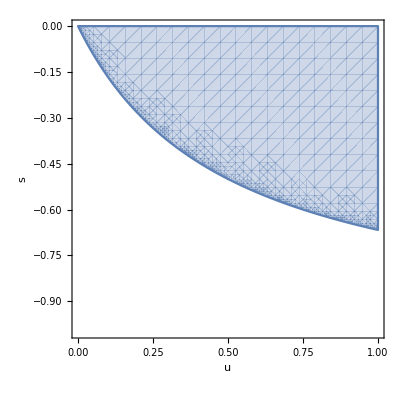

```mathematica
RegionPlot[stable1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
stable2=Reduce[{-1<eig2[[1]]<1,-1<eig2[[2]]<1,0<u<1,-1<s<0}]
```

False

```mathematica
stable3=Reduce[{-1<eig3[[1]]<1,-1<eig3[[2]]<1,0<u<1,-1<s<0}]
```

0<u<1&&-1<s<-(2 u)/(1+2 u)

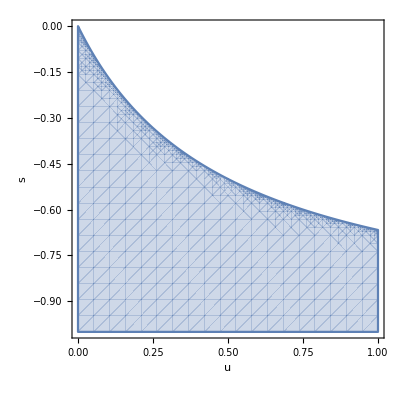

```mathematica
RegionPlot[stable3,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

## Analysis

We analyze the model for different ploidies: n = 1 to 9.  For n ≥ 10 the analysis takes several hours.

### Haploidy

```mathematica
n=1
```

1

```mathematica
sol=getsols[n,s,u]
```

{{f_0→0},{f_0→(s+u+s u)/(s (1+u))}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0},{f_0→0.99001}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-u/(1+u)}

```mathematica
jac=getjac[n,s,u]
```

{{-u+(s f_0)/((1+s) (1-f_0)+f_0)^2+1/((1+s) (1-f_0)+f_0)}}

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify
```

{{{1/(1+s)-u}},{{1+u+u^2+s (1+u)^2}}}

```mathematica
stab=Table[Reduce[{-1<jacsol[[i]]<1,0<u<1,-1<s<0}],{i,1,Length[sol]}]
```

{0<u<1&&-u/(1+u)<s<0,0<u<1&&-1<s<-u/(1+u)}

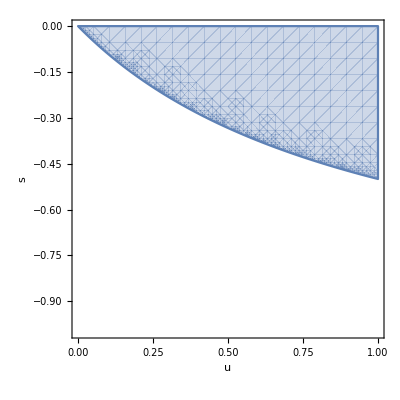

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

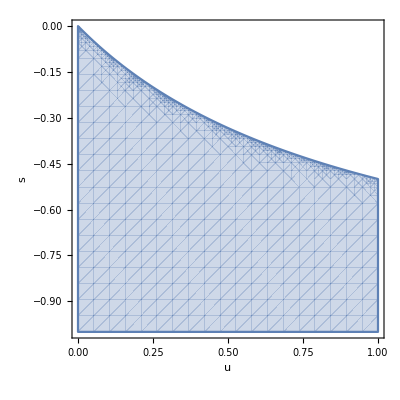

```mathematica
RegionPlot[stab[[2]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Diploidy

```mathematica
n=2
```

2

```mathematica
sol=getsols[n,s,u]//Simplify
```

{{f_0→0,f_1→0},{f_0→0,f_1→(s+2 u+2 s u)/(s+s u)},{f_0→(s+2 u+2 s u)^2/(s+2 s u)^2,f_1→-(4 u (s+2 u+2 s u))/(s+2 s u)^2}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0},{f_0→0,f_1→0.981019},{f_0→0.960478,f_1→0.0391234}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(2 u)/(1+2 u),0<u<1&&-1<s≤-(2 u)/(1+2 u)}

```mathematica
jac=getjac[n,s,u]//Simplify
```

{{-2 u+2/(2+2 s-2 s f_0-s f_1)+(4 s f_0)/(-2-2 s+2 s f_0+s f_1)^2,(2 s f_0)/(-2 (1+s)+2 s f_0+s f_1)^2},{2 (u+(s (2+s) f_1)/(-2-2 s+2 s f_0+s f_1)^2),-u+(2+s)/(2+2 s-2 s f_0-s f_1)+(s (2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1)^2}}

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify
```

{{{1/(1+s)-2 u,0},{2 u,(2+s)/(2+2 s)-u}},{{-(2 (-1+u+s u))/(2+s),0},{(2 (2 u (2+u)+s (1+4 u+2 u^2)))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)}},{{((1+s) (4 u^2+s (1+2 u)^2))/s,(s+2 u+2 s u)^2/(2 s)},{-(2 (1+s) u (s+4 u+2 s u))/s,1-u-6 u^2-(4 u^2)/s+s (1/2-2 u^2)}}}

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify
```

{{(2+s-2 u-2 s u)/(2+2 s),(1-2 (1+s) u)/(1+s)},{-(2 (-1+u+s u))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)},{(1+s) (1+2 u),1+u+2 u^2+1/2 s (1+2 u)^2}}

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{0<u<1&&-(2 u)/(1+2 u)<s<0,False,0<u<1&&-1<s<-(2 u)/(1+2 u)}

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

-Graphics-

```mathematica
RegionPlot[stab[[3]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

-Graphics-

### Triploidy

```mathematica
n=3
```

3

```mathematica
sol=getsols[n,s,u]//Simplify
```

{{f_0→0,f_1→0,f_2→0},{f_0→0,f_1→0,f_2→(s+3 u+3 s u)/(s+s u)},{f_0→0,f_1→(s+3 u+3 s u)^2/(s+2 s u)^2,f_2→-(2 (3+s) u (s+3 u+3 s u))/(s+2 s u)^2},{f_0→(s+3 u+3 s u)^3/(s+3 s u)^3,f_1→-(9 u (s+3 u+3 s u)^2)/(s+3 s u)^3,f_2→(27 u^2 (s+3 u+3 s u))/(s+3 s u)^3}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0},{f_0→0,f_1→0,f_2→0.972028},{f_0→0,f_1→0.942953,f_2→0.0562089},{f_0→0.912926,f_1→0.0844433,f_2→0.0026036}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(3 u)/(1+3 u),0<u<1&&-1<s≤-(3 u)/(1+3 u),0<u<1&&-1<s≤-(3 u)/(1+3 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify
```

{{(3+s-6 u-6 s u)/(3+3 s),(3+2 s-3 u-3 s u)/(3+3 s),(1-3 (1+s) u)/(1+s)},{(3+s-3 u-3 s u)/(3+2 s),(3-6 (1+s) u)/(3+2 s),(3 (1+u+u^2)+s (3+4 u+3 u^2))/(3+2 s)},{-(3 (-1+u+s u))/(3+s),(3 (1+s) (1+2 u))/(3+s),(3+2 s+3 u+5 s u+6 u^2+6 s u^2)/(3+s)},{(1+s) (1+3 u),1+u+3 u^2+1/3 s (1+3 u)^2,1+2 u+s (2/3+2 u)}}

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤2/3&&-(3 u)/(1+3 u)<s<0)||(2/3<u<1&&-(3 u)/(1+3 u)<s<(2-3 u)/(-1+3 u)),False,False,0<u<1&&-1<s<-(3 u)/(1+3 u)}

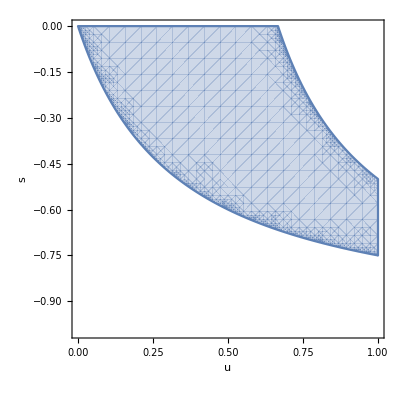

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

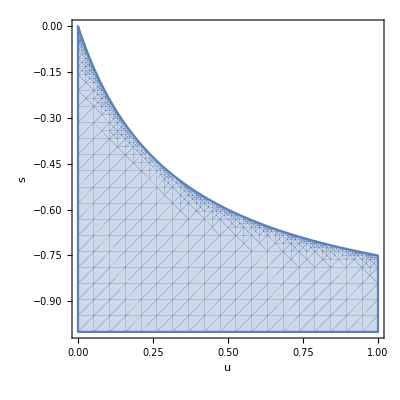

```mathematica
RegionPlot[stab[[4]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Tetraploidy

```mathematica
n=4
```

4

```mathematica
sol=getsols[n,s,u]//Simplify
```

{{f_0→0,f_1→0,f_2→0,f_3→0},{f_0→0,f_1→0,f_2→0,f_3→(s+4 u+4 s u)/(s+s u)},{f_0→0,f_1→0,f_2→(s+4 u+4 s u)^2/(s+2 s u)^2,f_3→-(4 (2+s) u (s+4 u+4 s u))/(s+2 s u)^2},{f_0→0,f_1→(s+4 u+4 s u)^3/(s+3 s u)^3,f_2→-(3 (4+s) u (s+4 u+4 s u)^2)/(s+3 s u)^3,f_3→(3 (4+s)^2 u^2 (s+4 u+4 s u))/(s+3 s u)^3},{f_0→(s+4 u+4 s u)^4/(s+4 s u)^4,f_1→-(16 u (s+4 u+4 s u)^3)/(s+4 s u)^4,f_2→(96 u^2 (s+4 u+4 s u)^2)/(s+4 s u)^4,f_3→-(256 u^3 (s+4 u+4 s u))/(s+4 s u)^4}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0},{f_0→0,f_1→0,f_2→0,f_3→0.963037},{f_0→0,f_1→0,f_2→0.92559,f_3→0.0729718},{f_0→0,f_1→0.887827,f_2→0.107755,f_3→0.00435938},{f_0→0.849911,f_1→0.141064,f_2→0.00877992,f_3→0.000242875}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(4 u)/(1+4 u),0<u<1&&-1<s≤-(4 u)/(1+4 u),0<u<1&&-1<s≤-(4 u)/(1+4 u),0<u<1&&-1<s≤-(4 u)/(1+4 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify
```

{{(4+s-12 u-12 s u)/(4+4 s),(4+3 s-4 u-4 s u)/(4+4 s),(1-4 (1+s) u)/(1+s),(2+s-4 u-4 s u)/(2+2 s)},{(4+s-8 u-8 s u)/(4+3 s),(4+2 s-4 u-4 s u)/(4+3 s),-(4 (-1+3 (1+s) u))/(4+3 s),(4 (1+u+u^2)+s (4+5 u+4 u^2))/(4+3 s)},{(2-4 (1+s) u)/(2+s),(4+s-4 u-4 s u)/(4+2 s),(2 (1+s) (1+2 u))/(2+s),(4+3 s+4 u+6 s u+8 u^2+8 s u^2)/(4+2 s)},{(4 (1+s) (1+3 u))/(4+s),-(4 (-1+u+s u))/(4+s),(4 (1+u+3 u^2)+s (2+7 u+12 u^2))/(4+s),(4+3 s+8 u+8 s u)/(4+s)},{(1+s) (1+4 u),1/2 (2+s+4 u+4 s u),1+3 u+s (3/4+3 u),1+u+4 u^2+1/4 s (1+4 u)^2}}

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤1/2&&-(4 u)/(1+4 u)<s<0)||(1/2<u<1&&-(4 u)/(1+4 u)<s<(2-4 u)/(-1+4 u)),False,False,False,0<u<1&&-1<s<-(4 u)/(1+4 u)}

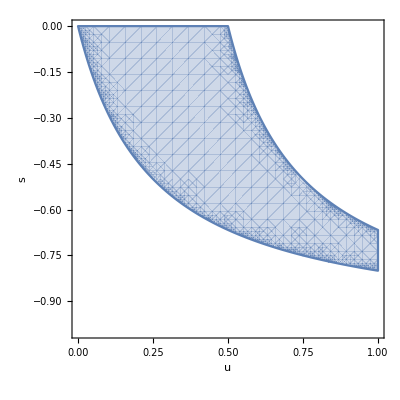

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

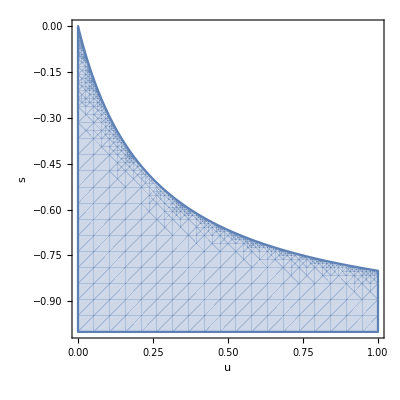

```mathematica
RegionPlot[stab[[5]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Pentaploidy

```mathematica
n=5
```

5

```mathematica
sol=getsols[n,s,u]//Simplify;
```

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.954046},{f_0→0,f_1→0,f_2→0,f_3→0.908388,f_4→0.089412},{f_0→0,f_1→0,f_2→0.863192,f_3→0.130157,f_4→0.00654191},{f_0→0,f_1→0.818613,f_2→0.168009,f_3→0.0129305,f_4→0.0004423},{f_0→0.774795,f_1→0.202826,f_2→0.0212383,f_3→0.00111195,f_4→0.0000291087}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(5 u)/(1+5 u),0<u<1&&-1<s≤-(5 u)/(1+5 u),0<u<1&&-1<s≤-(5 u)/(1+5 u),0<u<1&&-1<s≤-(5 u)/(1+5 u),0<u<1&&-1<s≤-(5 u)/(1+5 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify
```

{{(5+s-20 u-20 s u)/(5+5 s),(5+2 s-15 u-15 s u)/(5+5 s),(5+3 s-10 u-10 s u)/(5+5 s),(5+4 s-5 u-5 s u)/(5+5 s),(1-5 (1+s) u)/(1+s)},{(5+s-15 u-15 s u)/(5+4 s),(5+2 s-10 u-10 s u)/(5+4 s),(5+3 s-5 u-5 s u)/(5+4 s),-(5 (-1+4 (1+s) u))/(5+4 s),(5 (1+u+u^2)+s (5+6 u+5 u^2))/(5+4 s)},{-(5 (-1+3 (1+s) u))/(5+3 s),(5+2 s-5 u-5 s u)/(5+3 s),(5+s-10 u-10 s u)/(5+3 s),(5 (1+s) (1+2 u))/(5+3 s),(5 (1+u+2 u^2)+s (4+7 u+10 u^2))/(5+3 s)},{(5 (1+s) (1+3 u))/(5+2 s),-(5 (-1+2 (1+s) u))/(5+2 s),(5+s-5 u-5 s u)/(5+2 s),(5 (1+u+3 u^2)+s (3+8 u+15 u^2))/(5+2 s),(5+4 s+10 u+10 s u)/(5+2 s)},{(5 (1+s) (1+4 u))/(5+s),-(5 (-1+u+s u))/(5+s),(5+3 s+10 u+10 s u)/(5+s),(5+4 s+15 u+15 s u)/(5+s),(5 (1+u+4 u^2)+s (2+9 u+20 u^2))/(5+s)},{(1+s) (1+5 u),1+2 u+s (2/5+2 u),1+3 u+s (3/5+3 u),1+4 u+s (4/5+4 u),1+u+5 u^2+1/5 s (1+5 u)^2}}

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤2/5&&-(5 u)/(1+5 u)<s<0)||(2/5<u<1&&-(5 u)/(1+5 u)<s<(2-5 u)/(-1+5 u)),False,False,False,False,0<u<1&&-1<s<-(5 u)/(1+5 u)}

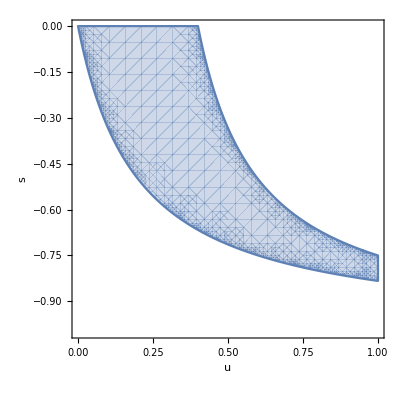

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

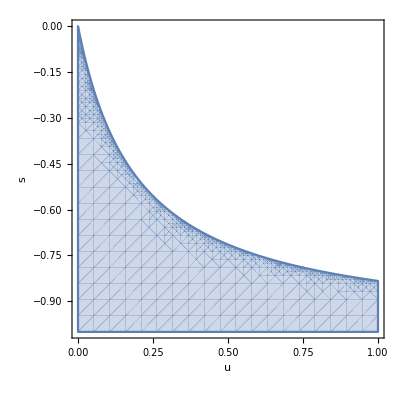

```mathematica
RegionPlot[stab[[6]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Hexaploidy

```mathematica
n=6
```

6

```mathematica
sol=getsols[n,s,u]//Simplify;
```

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.945055},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.891347,f_5→0.105529},{f_0→0,f_1→0,f_2→0,f_3→0.839017,f_4→0.151662,f_5→0.00913817},{f_0→0,f_1→0,f_2→0.788188,f_3→0.193298,f_4→0.0177768,f_5→0.000726608},{f_0→0,f_1→0.738968,f_2→0.230439,f_3→0.028744,f_4→0.0017927,f_5→0.0000559035},{f_0→0.691447,f_1→0.26313,f_2→0.0417225,f_3→0.00352833,f_4→0.000167838,f_5→4.25805×10^-6}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(6 u)/(1+6 u),0<u<1&&-1<s≤-(6 u)/(1+6 u),0<u<1&&-1<s≤-(6 u)/(1+6 u),0<u<1&&-1<s≤-(6 u)/(1+6 u),0<u<1&&-1<s≤-(6 u)/(1+6 u),0<u<1&&-1<s≤-(6 u)/(1+6 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify
```

{{(6+s-30 u-30 s u)/(6+6 s),(6+5 s-6 u-6 s u)/(6+6 s),(1-6 (1+s) u)/(1+s),(3+2 s-6 u-6 s u)/(3+3 s),(2+s-6 u-6 s u)/(2+2 s),(3+s-12 u-12 s u)/(3+3 s)},{(6+s-24 u-24 s u)/(6+5 s),(6+4 s-6 u-6 s u)/(6+5 s),(3 (2+s-4 u-4 s u))/(6+5 s),-(6 (-1+5 (1+s) u))/(6+5 s),(2 (3+s-9 u-9 s u))/(6+5 s),(6 (1+u+u^2)+s (6+7 u+6 u^2))/(6+5 s)},{(6+3 s-6 u-6 s u)/(6+4 s),-(3 (-1+4 (1+s) u))/(3+2 s),(3+s-6 u-6 s u)/(3+2 s),(6+s-18 u-18 s u)/(6+4 s),(3 (1+s) (1+2 u))/(3+2 s),(6 (1+u+2 u^2)+s (5+8 u+12 u^2))/(6+4 s)},{(2 (1+s) (1+3 u))/(2+s),(2-6 (1+s) u)/(2+s),(6+2 s-6 u-6 s u)/(6+3 s),(6+s-12 u-12 s u)/(6+3 s),(6+4 s+6 u+9 s u+18 u^2+18 s u^2)/(6+3 s),(6+5 s+12 u+12 s u)/(6+3 s)},{(3 (1+s) (1+4 u))/(3+s),(3-6 (1+s) u)/(3+s),(6+s-6 u-6 s u)/(6+2 s),(3+2 s+6 u+6 s u)/(3+s),(6+5 s+18 u+18 s u)/(6+2 s),(6+3 s+6 u+10 s u+24 u^2+24 s u^2)/(6+2 s)},{(6 (1+s) (1+5 u))/(6+s),-(6 (-1+u+s u))/(6+s),(3 (2+s+4 u+4 s u))/(6+s),(2 (3+9 u+s (2+9 u)))/(6+s),(6+5 s+24 u+24 s u)/(6+s),(6 (1+u+5 u^2)+s (2+11 u+30 u^2))/(6+s)},{(1+s) (1+6 u),1/2 (2+s+6 u+6 s u),1/3 (3+s+6 u+6 s u),1+4 u+s (2/3+4 u),1+5 u+s (5/6+5 u),1+u+6 u^2+1/6 s (1+6 u)^2}}

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤1/3&&-(6 u)/(1+6 u)<s<0)||(1/3<u<1&&-(6 u)/(1+6 u)<s<(2-6 u)/(-1+6 u)),False,False,False,False,False,0<u<1&&-1<s<-(6 u)/(1+6 u)}

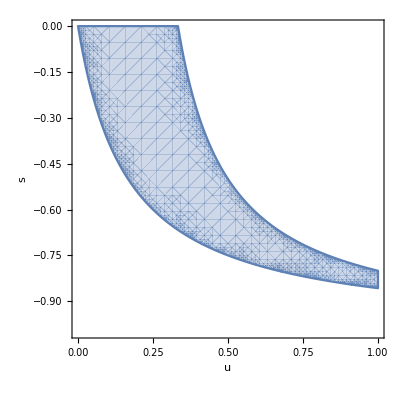

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

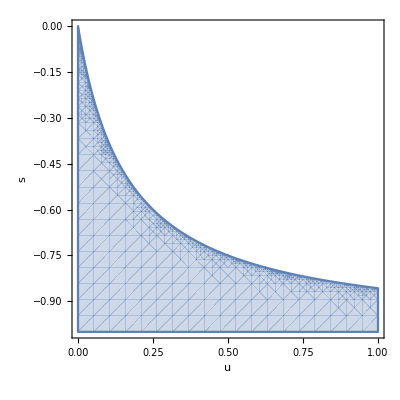

```mathematica
RegionPlot[stab[[7]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Heptaploidy

```mathematica
n=7
```

7

```mathematica
sol=getsols[n,s,u]//Simplify;
```

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0.936064},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.874468,f_6→0.121324},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.815297,f_5→0.172283,f_6→0.0121352},{f_0→0,f_1→0,f_2→0,f_3→0.758619,f_4→0.21698,f_5→0.0232726,f_6→0.0011094},{f_0→0,f_1→0,f_2→0.704478,f_3→0.255627,f_4→0.0371028,f_5→0.00269262,f_6→0.0000977046},{f_0→0,f_1→0.652904,f_2→0.288476,f_3→0.053108,f_4→0.00521445,f_5→0.000287991,f_6→8.48298×10^-6},{f_0→0.603908,f_1→0.315811,f_2→0.0707794,f_3→0.00881281,f_4→0.000658374,f_5→0.0000295109,f_6→7.34885×10^-7}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u),0<u<1&&-1<s≤-(7 u)/(1+7 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤2/7&&-(7 u)/(1+7 u)<s<0)||(2/7<u<1&&-(7 u)/(1+7 u)<s<(2-7 u)/(-1+7 u)),False,False,False,False,False,False,0<u<1&&-1<s<-(7 u)/(1+7 u)}

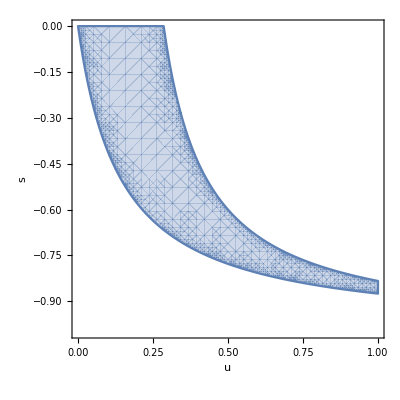

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

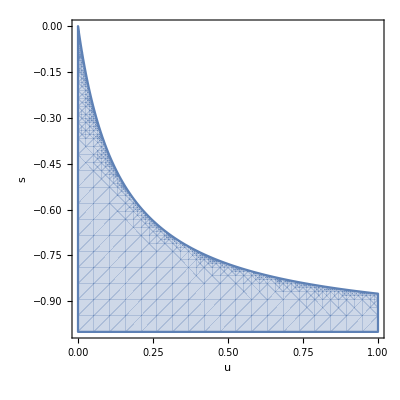

```mathematica
RegionPlot[stab[[8]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Octoploidy

```mathematica
n=8
```

8

```mathematica
sol=getsols[n,s,u]//Simplify;
```

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0,f_7→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0,f_7→0.927073},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0.85775,f_7→0.136796},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.792029,f_6→0.192033,f_7→0.0155199},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.729889,f_5→0.239102,f_6→0.0293724,f_7→0.00160367},{f_0→0,f_1→0,f_2→0,f_3→0.671289,f_4→0.278498,f_5→0.0462163,f_6→0.00383476,f_7→0.000159093},{f_0→0,f_1→0,f_2→0.616169,f_3→0.31074,f_4→0.0652957,f_5→0.00731762,f_6→0.000461294,f_7→0.000015509},{f_0→0.516059,f_1→0.355903,f_2→0.107385,f_3→0.0185146,f_4→0.0019951,f_5→0.000137593,f_6→5.93075×10^-6,f_7→1.46078×10^-7},{f_0→0,f_1→0.564455,f_2→0.336362,f_3→0.0859027,f_4→0.0121881,f_5→0.00103756,f_6→0.0000529962,f_7→1.50384×10^-6}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u),0<u<1&&-1<s≤-(8 u)/(1+8 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify;
```

$Aborted

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤1/4&&-(8 u)/(1+8 u)<s<0)||(1/4<u<1&&-(8 u)/(1+8 u)<s<(2-8 u)/(-1+8 u)),False,False,False,False,False,False,0<u<1&&-1<s<-(8 u)/(1+8 u),False}

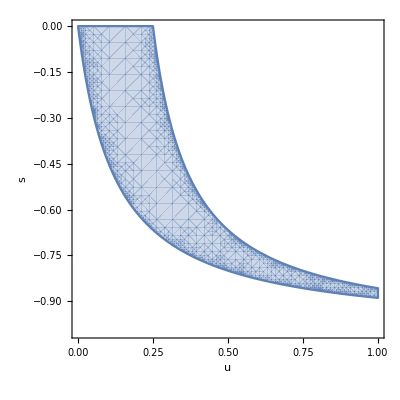

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

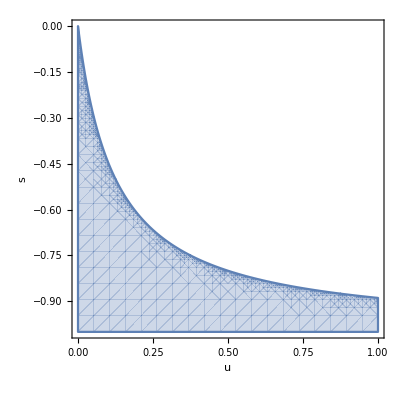

```mathematica
RegionPlot[stab[[8]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### Nonaploidy

```mathematica
n=9
```

9

```mathematica
sol=getsols[n,s,u]//Simplify;
```

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0,f_7→0,f_8→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0,f_7→0,f_8→0.918082},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0,f_7→0.841193,f_8→0.151946},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0.769208,f_7→0.210925,f_8→0.0192794},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.701984,f_6→0.259711,f_7→0.0360317,f_8→0.00222176},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.639363,f_5→0.299158,f_6→0.0559903,f_7→0.00523958,f_8→0.00024516},{f_0→0,f_1→0,f_2→0,f_3→0.581173,f_4→0.330111,f_5→0.0781275,f_6→0.00986158,f_7→0.000700183,f_8→0.000026514},{f_0→0.431339,f_1→0.380179,f_2→0.148928,f_3→0.0340314,f_4→0.00499917,f_5→0.000489581,f_6→0.0000319639,f_7→1.34156×10^-6,f_8→3.28456×10^-8},{f_0→0,f_1→0,f_2→0.527233,f_3→0.353401,f_4→0.101521,f_5→0.0162021,f_6→0.00155145,f_7→0.0000891369,f_8→2.84514×10^-6},{f_0→0,f_1→0.477353,f_2→0.369832,f_3→0.125356,f_4→0.0242801,f_5→0.00293925,f_6→0.00022772,f_7→0.0000110267,f_8→3.05106×10^-7}}

```mathematica
valid=Table[Reduce[Flatten[{Table[0≤Values[sol[[j]][[i]]]≤1,{i,1,n}],0<u<1,-1<s<0}]],{j,1,Length[sol]}]
```

{0<u<1&&-1<s<0,0<u<1&&-1<s≤-(2 u)/(1+2 u),0<u<1&&-1<s≤-(2 u)/(1+2 u)}

```mathematica
jac=getjac[n,s,u]//Simplify;
```

```mathematica
jacsol=Table[jac/.sol[[i]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
eig=Table[Eigenvalues[jacsol[[i]]],{i,1,Length[sol]}]//Simplify;
```

```mathematica
stab=Table[Reduce[Flatten[Table[{-1<eig[[i]][[j]]<1,0<u<1,-1<s<0},{j,1,n}]]],{i,1,Length[sol]}]
```

{(0<u≤2/9&&-(9 u)/(1+9 u)<s<0)||(2/9<u<1&&-(9 u)/(1+9 u)<s<(2-9 u)/(-1+9 u)),False,False,False,False,False,False,0<u<1&&-1<s<-(9 u)/(1+9 u),False,False}

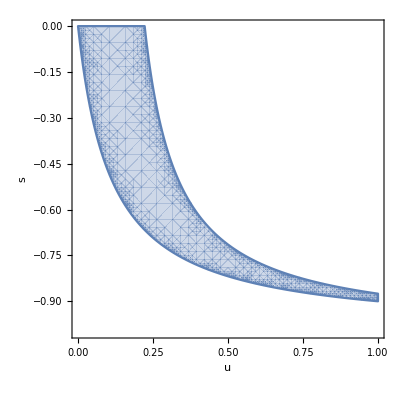

```mathematica
RegionPlot[stab[[1]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

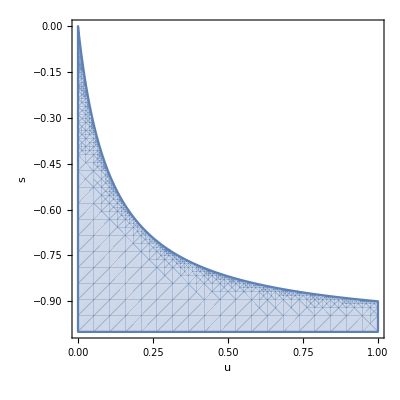

```mathematica
RegionPlot[stab[[8]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

## Results

These results are enough to make the following generalizations. 

1. For every ploidy n there are n+1 equilibria.  Two of these equilibria are stable for meaningful values of u and s (i.e., 0 < u < 1 and –1 < s < 0).  The other equilibria are not stable for meaningful values of u and s.

2. The first stable equilibrium has the form: f_0=f_1=…=f_(n-1)=0,f_n=1.  In other words, the deleterious mutation goes to fixation.  The mean fitness for this equilibrium is: ŵ=1-s.  For low values of u (0<u≤2/n), this equilibrium is only stable for mutations of very small effect (-(n u)/(1+n u)<s<0). 

3. The second stable equilibrium has the form: f_k=(-1)^k((n
k)n^k u^k (s+n u+n s u)^(n-k))/(s+n s u)^n.  The mean fitness for this equilibrium is: ŵ=1/(1+n u).  For low values of u (0<u≤2/n), this equilibrium is always stable except for mutations of very small effect (-1<s<(n u)/(1+n u)). 

4. The other n–1 equilibria have the form: 
f_0=0
f_0=0 and f_1=0
f_0=0,f_1=0 and f_2=0
… 
f_0=0,f_1=0,… f_(n-2)=0

Below we illustrate these results, first for n=15 and then for n=45.

```mathematica
eq[n_,s_,u_]:=Table[Subscript[f, k]->(-1)^k(Binomial[n,k] n^k u^k (s+n u+n s u)^(n-k))/(s+n s u)^n,{k,0,n-1}]
```

```mathematica
nextf15=ff[15,s,u];
```

```mathematica
eq15=eq[15,s,u]
```

{f_0→(s+15 u+15 s u)^15/(s+15 s u)^15,f_1→-(225 u (s+15 u+15 s u)^14)/(s+15 s u)^15,f_2→(23625 u^2 (s+15 u+15 s u)^13)/(s+15 s u)^15,f_3→-(1535625 u^3 (s+15 u+15 s u)^12)/(s+15 s u)^15,f_4→(69103125 u^4 (s+15 u+15 s u)^11)/(s+15 s u)^15,f_5→-(2280403125 u^5 (s+15 u+15 s u)^10)/(s+15 s u)^15,f_6→(57010078125 u^6 (s+15 u+15 s u)^9)/(s+15 s u)^15,f_7→-(1099480078125 u^7 (s+15 u+15 s u)^8)/(s+15 s u)^15,f_8→(16492201171875 u^8 (s+15 u+15 s u)^7)/(s+15 s u)^15,f_9→-(192409013671875 u^9 (s+15 u+15 s u)^6)/(s+15 s u)^15,f_10→(1731681123046875 u^10 (s+15 u+15 s u)^5)/(s+15 s u)^15,f_11→-(11806916748046875 u^11 (s+15 u+15 s u)^4)/(s+15 s u)^15,f_12→(59034583740234375 u^12 (s+15 u+15 s u)^3)/(s+15 s u)^15,f_13→-(204350482177734375 u^13 (s+15 u+15 s u)^2)/(s+15 s u)^15,f_14→(437893890380859375 u^14 (s+15 u+15 s u))/(s+15 s u)^15}

```mathematica
nextf15eq=nextf15/.eq15//Simplify
```

{(s+15 u+15 s u)^15/(s+15 s u)^15,-(225 u (s+15 u+15 s u)^14)/(s+15 s u)^15,(23625 u^2 (s+15 u+15 s u)^13)/(s+15 s u)^15,-(1535625 u^3 (s+15 u+15 s u)^12)/(s+15 s u)^15,(69103125 u^4 (s+15 u+15 s u)^11)/(s+15 s u)^15,-(2280403125 u^5 (s+15 u+15 s u)^10)/(s+15 s u)^15,(57010078125 u^6 (s+15 u+15 s u)^9)/(s+15 s u)^15,-(1099480078125 u^7 (s+15 u+15 s u)^8)/(s+15 s u)^15,(16492201171875 u^8 (s+15 u+15 s u)^7)/(s+15 s u)^15,-(192409013671875 u^9 (s+15 u+15 s u)^6)/(s+15 s u)^15,(1731681123046875 u^10 (s+15 u+15 s u)^5)/(s+15 s u)^15,-(11806916748046875 u^11 (s+15 u+15 s u)^4)/(s+15 s u)^15,(59034583740234375 u^12 (s+15 u+15 s u)^3)/(s+15 s u)^15,-(204350482177734375 u^13 (s+15 u+15 s u)^2)/(s+15 s u)^15,(437893890380859375 u^14 (s+15 u+15 s u))/(s+15 s u)^15,-(437893890380859375 u^15)/(s+15 s u)^15}

```mathematica
Table[Simplify[nextf15eq[[i]]==Values[eq15[[i]]]],{i,1,15}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
w̄[15,s]/.Subscript[f, 15]->cum[15]/.eq15//Simplify
```

1/(1+15 u)

```mathematica
nextf45=ff[45,s,u];
```

```mathematica
eq45=eq[45,s,u];
```

```mathematica
w̄[45,s]/.Subscript[f, 45]->cum[45]/.eq45//Simplify
```

1/(1+45 u)